1-(251 t)/252+(2875 t^2)/3024-(4625 t^3)/6048+(625 t^4)/1512-(625 t^5)/6048

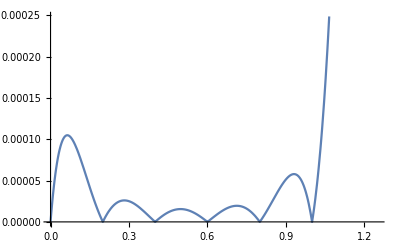

```mathematica
(* Да се реши интерполационната задача на Лагранж за f(t)=1/(1+t), 0≤t≤1, Xk = k/n, k =0,1,...,n *)
n=5;
Do[x[k]=k/n,{k,0,n}];
w[t_]:=∏_(k=0)^n (t-x[k]);
Do[v[k_,t_]:=w[t]/(t-x[k]), {k,0,n}];
Do[l[k_,t_]:=v[k,t]/Simplify[v[k,t]/.t->x[k]],{k,0,n}];
L[f_,t_]:=∑_(k=0)^n (l[k,t]*f[x[k]]);
f[t_]:=1/(1+t);
a=Expand[L[f,t]]
Plot[Abs[f[t]-a],{t,0,1.25}]
```